```mathematica
(* 1 - Botswana, 2 - Zimbabwe *)
(* Human parameters *)
Subscript[N, 1]=8  10^6;
Subscript[N, 2]=2 10^7 ;
Subscript[γ, 1]=N@(1/14);
Subscript[γ, 2]=N@(1/14);

Subscript[p, 11]=0.85;
Subscript[p, 12]=1-Subscript[p, 11];
Subscript[p, 22]=0.85;
Subscript[p, 21]=1-Subscript[p, 22];
Subscript[H, 1]=Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2];
Subscript[H, 2]=Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2];

(* Mosquito parameters *) 
Subscript[M, 1]=7.5 Subscript[N, 1];(*RandomReal[{10^7,10^8}]; *)
Subscript[M, 2]=8 Subscript[N, 2];(*RandomReal[{10^7,10^8}] ;*)
Subscript[μ, 1]=0.0476190476190476;
Subscript[μ, 2]=0.0666666666666667;
τ=10.;

(* Infectivity parameters *)
Subscript[a, 1]=0.12;
Subscript[a, 2]=0.18;
Subscript[β, vh]=0.5;
Subscript[β, hv]=0.1;


(* Control parameters *)
κ=0;
Subscript[u, 1]=0.15;
Subscript[u, 2]=0.3;


Subscript[b, 11]=Subscript[β, vh](Subscript[p, 11] E^(-Subscript[μ, 1]τ)Subscript[a, 1] Subscript[M, 1])/Subscript[H, 1];
Subscript[b, 12]=Subscript[β, vh](Subscript[p, 12] E^(-Subscript[μ, 2]τ)Subscript[a, 2] Subscript[M, 2])/Subscript[H, 2];
Subscript[b, 21]=Subscript[β, vh](Subscript[p, 21] E^(-Subscript[μ, 1]τ)Subscript[a, 1] Subscript[M, 1])/Subscript[H, 1];
Subscript[b, 22]=Subscript[β, vh](Subscript[p, 22] E^(-Subscript[μ, 2]τ)Subscript[a, 2] Subscript[M, 2])/Subscript[H, 2];

Subscript[c, 11]=Subscript[β, hv](Subscript[p, 11] Subscript[a, 1] Subscript[N, 1])/Subscript[H, 1];
Subscript[c, 12]=Subscript[β, hv](Subscript[p, 21] Subscript[a, 1] Subscript[N, 2])/Subscript[H, 1];
Subscript[c, 21]=Subscript[β, hv](Subscript[p, 12] Subscript[a, 2] Subscript[N, 1])/Subscript[H, 2];
Subscript[c, 22]=Subscript[β, hv](Subscript[p, 22] Subscript[a, 2] Subscript[N, 2])/Subscript[H, 2];

Subscript[Imax, 1]=0.1;
Subscript[Imax, 2]=0.14;

equilibrium = {Subscript[x, 1],Subscript[x, 2]}/.NSolve[
(1-Subscript[x, 1])(1-κ Subscript[u, 1])(Subscript[b, 11] Subscript[y, 1]+Subscript[b, 12] Subscript[y, 2]) - Subscript[γ, 1] Subscript[x, 1]==0&&
(1-Subscript[x, 2])(1-κ Subscript[u, 2])(Subscript[b, 21] Subscript[y, 1]+Subscript[b, 22] Subscript[y, 2]) - Subscript[γ, 2] Subscript[x, 2]==0&&
 (1-Subscript[y, 1])(Subscript[c, 11](1-κ Subscript[u, 1])Subscript[x, 1]+Subscript[c, 12](1-κ Subscript[u, 2])Subscript[x, 2]) - Subscript[μ, 1] Subscript[y, 1]==0&&

(1-Subscript[y, 2])(Subscript[c, 21](1-κ Subscript[u, 1])Subscript[x, 1]+Subscript[c, 22](1-κ Subscript[u, 2])Subscript[x, 2]) - Subscript[μ, 2] Subscript[y, 2]==0&&
Subscript[x, 1]>=0&&Subscript[y, 1]>=0&&Subscript[x, 2]>=0&&Subscript[y, 2]>=0&&
Subscript[x, 1]≤1&&Subscript[y, 1]≤1&&Subscript[x, 2]≤1&&Subscript[y, 2]≤1,
{Subscript[x, 1],Subscript[x, 2],Subscript[y, 1],Subscript[y, 2]},Reals]⟦1⟧
equilibrium⟦1⟧<=Subscript[Imax, 1] && equilibrium⟦2⟧<= Subscript[Imax, 2]
```

{0.012522,0.0214335}

True

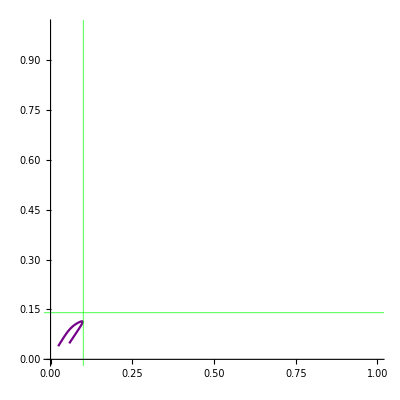

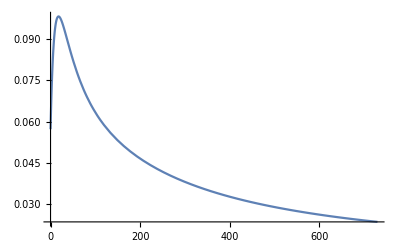

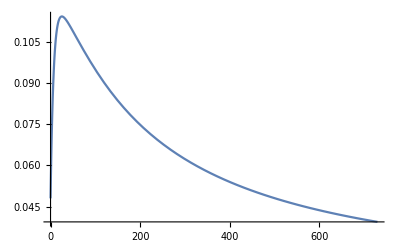

patch-dynamics-irreducible-2.csv

{0.0234278,0.0393959}

```mathematica
{x10,x20,y10,y20}={0.05720000,0.04800000,0.05200000,0.04400000};
tMax=730;
numericalIntegration =NDSolve[{
Subscript[x, 1]'[t]==(1-Subscript[x, 1][t])(1-κ Subscript[u, 1])(Subscript[b, 11] Subscript[y, 1][t]+Subscript[b, 12] Subscript[y, 2][t]) - Subscript[γ, 1] Subscript[x, 1][t],
Subscript[x, 2]'[t]==(1-Subscript[x, 2][t])(1-κ Subscript[u, 2])(Subscript[b, 21] Subscript[y, 1][t]+Subscript[b, 22] Subscript[y, 2][t]) - Subscript[γ, 2] Subscript[x, 2][t],
Subscript[y, 1]'[t]==(1-Subscript[y, 1][t])(Subscript[c, 11](1-κ Subscript[u, 1])Subscript[x, 1][t]+Subscript[c, 12](1-κ Subscript[u, 2])Subscript[x, 2][t]) - Subscript[μ, 1] Subscript[y, 1][t],
Subscript[y, 2]'[t]==(1-Subscript[y, 2][t])(Subscript[c, 21](1-κ Subscript[u, 1])Subscript[x, 1][t]+Subscript[c, 22](1-κ Subscript[u, 2])Subscript[x, 2][t]) - Subscript[μ, 2] Subscript[y, 2][t],
Subscript[x, 1][0]==x10,Subscript[x, 2][0]==x20,Subscript[y, 1][0]==y10,Subscript[y, 2][0]==y20},
{Subscript[x, 1],Subscript[x, 2],Subscript[y, 1],Subscript[y, 2]},
{t,0,tMax}
];
{botswana,zimbabwe}={Subscript[x, 1],Subscript[x, 2]}/.numericalIntegration⟦1⟧;
solutionPlot=ParametricPlot[{botswana[t],zimbabwe[t]},{t,0,tMax},PlotRange->{{0,1},{0,1}},GridLines->{{Subscript[Imax, 1]},{Subscript[Imax, 2]}},GridLinesStyle->Directive[Green,Thick],ColorFunction->Function[{x,y,tscaled},Blend[{Red,Blue},Power[tscaled, 0.3]]]];
Show[{solutionPlot}]
Plot[botswana[t],{t,0,tMax},PlotRange->All]
Plot[zimbabwe[t],{t,0,tMax},PlotRange->All]
humanSolutions = (<|"t"->#⟦1⟧,"x1"->#⟦2⟧,"x2"->#[[3]]|>)&/@Table[{t,botswana[t], zimbabwe[t]},{t,0,tMax}] //Dataset;
SetDirectory[NotebookDirectory[]];
Export["patch-dynamics-irreducible-1.csv",humanSolutions]
{botswana[tMax], zimbabwe[tMax]}
```

```mathematica
humanSolutions = ({#⟦1⟧,#⟦2⟧,{Subscript[x, 1],Subscript[x, 2]}/.(#⟦3⟧⟦1⟧)}&)/@equilibriumPoints;
botswanaNormalized = ({#⟦1⟧,#⟦2⟧,#⟦3⟧⟦1⟧}&)/@humanSolutions;
zimbabweNormalized = ({#⟦1⟧,#⟦2⟧,#⟦3⟧⟦2⟧}&)/@humanSolutions;
```

```mathematica
(* Around 0.05720000,0.10200000,0.05200000,0.00000000 is interesting*)
(* No mobility and not in kernel with some mobility it is in kernel due to patch 1!*)
```

```mathematica
(* 0.09680000,0.07200000,0.00800000,0.03200000,-1.78731594e-06 is inside *)
(* 0.05720000,0.10200000,0.05200000,0.07200000,-3.80024633e-06 is outside *)
```